### Introduction and motivation

Working in an optics lab sometimes requires a precise control over the shape of the laser beam used at a specific point in the setup. You might need to control the diameter of the beam (and thus intensity) or the beams divergence angle. Or both. You might need to match the shapes (modes) of more then one light beam at more than one wavelength. You might need to determine which lens focal length is optimal for your given setup, which combination of two lenses will give you optimally collimated beam.

In order to address this questions you need to know two things - what is your initial beam and how will it change as you propagate it along the optical table. The goal of this script is to show you one possible approach towards visualizing the beam propagation across your setup. The idea is that allows for a visual optimization of the distances between components and their characteristics.

The underlying physics are: gaussian beam propagation and the related matrix formalism for beam propagation. Everything else is just having fun with many options Mathematica offers for plotting data.

It's a lot of useless text, but the idea is to present it as clearly as possible.

[In order for everything to work, you need to initialize the whole notebook. This is so that some definitions for functions I reference when plotting work. If sth breaks just go through the notebook and initialize the definitions one by one.]

[Throughout the notebook I use the word waist for two things which are not the same thing. One is actual waist size in the focus, other one is the diameter of the beam at a given point. What I mean at any time should be clear from the context.]

[Everything is in basic units (m,W,...), unless otherwise stated.]

If you don’t like sth or think I should add anything, let me know.

[According to a random Stack Exchange post, apparently using Manipulate[...] on Module[...] is not recommended, but I just don’t care.]

[Žiga Pušavec 2023-04- 11, UL FMF]

### 00 Measuring the initial beam going into the setup

Before doing anything else, one need to know what kind of beam do we initially have. Usually one will start with the beam coming out of the laser or out of a fibre (/fibre collimator). For our calculation the origin does not matter, we just want to know complex beam parameter at point z = 0. This is a point we mark on the table. All other distances z_1, z_2, ... are measured in relation to this point. In order to determined initial complex beam parameter at z = 0, we need to measure the beam waist w_1 and w_2 at two points z_1 and z_2 along the beam path. The further apart they are, the better. Two is the minimal number of points needed which will give you two possible solutions. If you want to be certain you picked the right solution, you can also perform the third measurement. Personally, I just check with an IR card if there is any focus between z_1 and z_2; if there is this usually corresponds to one of the solutions.

The intensity distribution of the cross-section of a gaussian beam looks like:

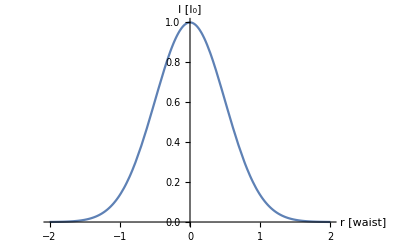

```mathematica
Plot[{Subscript[I, 0] E^((-2 r^2)/w^2)/.{w->1,Subscript[I, 0]->1}},{r,-2,2},AxesLabel->{"r [waist]","I [I_0]"},GridLines->{{-1,1},{1/E^2}}]
```

Note that I somewhat simplified the form. The only important thing is that we decide to define the size of the beam as the distance from the center to the point where the intensity drops to 1/E^2 of max value. This gives us waist w we will always refer to. (the diameter of the beam is twice this number, obviously).

We measure the beam waist with a knife-edge method. Initially you send your whole beam to a power meter, be careful you are not clipping part of the beam, use a short focusing lens if needed. The power meter should be further away than z_2 and would preferably not be moved between measurements. (If your beam at that point is too big for the active area of the power meter you can simply focus it with a 25 mm lens.) The idea now is that you slowly move a sharp edge across the beam at given point in the setup. More of the beam you cover, less power you detect on the power meter. You do this by attaching a sharp edge, a cheap razor blade, to a LINEAR translation stage. Initially, you put this edge close to the beam, so that the power only slightly drops. Move the whole translation stage a little back so the power goes back up and fix the translation stage to the table. Now move the razor across the beam in defined steps, writing down the razor movement and the detected optical power.

In a way, you are integrating the surface area under the line in the top graph. The amount of power on the detector is  “1 - your measurement”. Your data should look something like this:

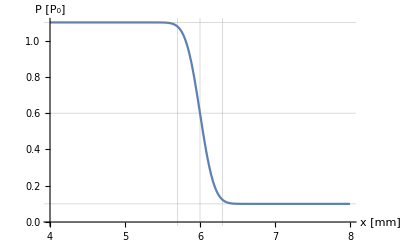

```mathematica
Plot[{P0/2 Erfc[(r-r0)/(w/√2)]+Poffset/.{w->0.3,P0->1,r0->6,Poffset->0.1}},{r,4,8},AxesLabel->{"x [mm]","P [P_0]"},GridLines->{{6-0.3,6,6+0.3},{0.1,0.5+0.1,1+0.1}}]
```

Now you only need to fit your data to the above model and get the unknown parameters. The r_0 will tell you how far away is the centre of the beam from where you started to measure the translation stage displacement. P_offset will tell you the offset of the power meter, P_0 - P_offset the max power you detect (good way to evaluate the quality of your fit). And the w_1 will tell you the waist of your beam. Mark it down as well as the distance z_1 from your reference point z = 0. This z_1 should the point exactly bellow the point where your razor cut the beam.

Now repeat the same measurement and fit at the next point z_2.

I write down the data in a quick Excel file, and then do the fitting in a python script. You can also do it directly in Mathematica, but I personally don’t like working with data files directly in Mathematica. However you do it, you should get four numbers: z_1 and w_1, z_2 and w_2. Now you have to use this numbers to find out what you beam actually is. Bellow, I am using an actual measurement I made at some point in the lab for a red beam at 8.5 cm and 60 cm away from a point I defined as z = 0.

```mathematica
Module[{λ,z1,w1,z2,w2,solutions},
λ=775 10^-9;

z1=261 10^-3;
w1=0.815309 10^-3;

z2=888 10^-3;
w2=0.952767 10^-3;
w[z_,w0_,λ_]:=w0 √(1+((z λ)/(π w0^2))^2);
solutions=NSolve[{w1==w0 √(1+(((z1-zwaist)λ)/(π w0^2))^2),w2==w0 √(1+(((z2-zwaist) λ)/(π w0^2))^2)},{w0,zwaist}];
Print[solutions]
]
```

{{w0→0.000691694,zwaist→-0.949194},{w0→0.0000879205,zwaist→0.549882}}

You will always get two solutions, one will probably represent a gaussian beam with a focus between z_1 and z_2, while the other one will have the focus out of this region. Best way to evaluate is to just plot them:

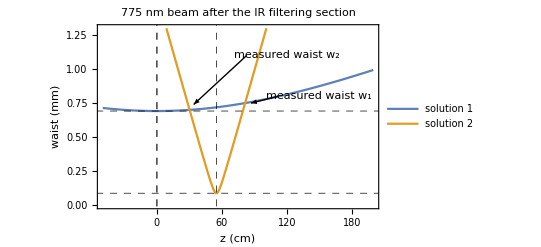

```mathematica
Module[{w0,zwaist,w01,w02,zwaist1,zwaist2,zcm,z,λ},
λ=775 10^-9;

w01=0.000691694;
zwaist1=0.000691694;

w02=0.0000879205;
zwaist2=0.549882;

z=zcm 10^-2;
Plot[{w[z-zwaist,w0,λ] 10^3/.{w0->w01,zwaist->zwaist1},w[z-zwaist,w0,λ] 10^3/.{w0->w02,zwaist->zwaist2}},{zcm,-50,200},Frame->True,Axes->None,FrameLabel->{"z (cm)","waist (mm)"},PlotLabel->Style["775 nm beam after the IR filtering section"],PlotLegends->{"solution 1","solution 2"},GridLines->{{0,zwaist1 10^2,zwaist2 10^2},{w01 10^3,w02 10^3}},GridLinesStyle->Directive[Black, Dashed],PlotRange->{0,1.3},
Epilog->{
Text[Framed["measured waist w_1"],{150,0.8}],
Arrow[{{112,0.8},{87,0.75}}],
Text[Framed["measured waist w_2"],{120,1.1}],
Arrow[{{83,1.1},{34,0.74}}]
}]

]
```

For this specific measurement, I checked the shape of the red beam along the beam path using a webcam. I did not find a focus between the two measurements. This means that the correct solution is the second one. This two parameters (w02, zwaist2) will tell me the complex beam parameter at z=0 and be the basis for all other calculations I do.

### 01 Basic plotting

The waist of a gaussian beam changes as the beam propagates through space. If you are interested, look at the derivation in standard photonics textbooks. This relationship is described by equation:

w(z) = w_0 √(1+(z/z_R)^2)

where  w_0 is waist in the focus of the beam (we call this also “waist”, sorry for the possible semantic confusion) and z_R is the Rayleigh lenght. If you are significantly more than z_R away from the focus, you are in the “far-field”, where the beam expands linearly with distance, think of it as a sort of point source.

```mathematica
w[z_,w0_,λ_]:=w0 √(1+((z λ)/(Pi w0^2))^2)
```

Let’s plot this. A generic gauss beam propagation:

Rayleigh lenght z_Reyleigh = 175.137 cm

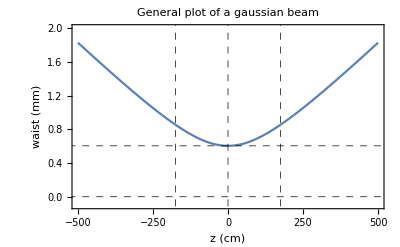

```mathematica
Module[{w0,zwaist,zcm,z,λ,zRayleigh},
λ=655 10^-9;
w0=0.0006042744933010027;
zwaist=1.3271969822526328;
zRayleigh = zR[w0,λ];
z=zcm 10^-2;

Print["Rayleigh lenght z_Reyleigh = ",zRayleigh 10^2," cm"];

Plot[{w[z,w0,λ] 10^3},{zcm,-500,500},Frame->True,Axes->None,FrameLabel->{"z (cm)","waist (mm)"},PlotLabel->Style["General plot of a gaussian beam"],PlotLegends->{},GridLines->{{0,zRayleigh 10^2,-zRayleigh 10^2},{0,w0 10^3}},GridLinesStyle->Directive[Black, Dashed],PlotRange->{-0.1,2}]
]
```

This initial plot assumes the focus of the gaussian beam is at z = 0. In general, this is not the case. It is arbitrary and left to you to decide the origin of your coordinate system. Lets say that the waist is z_0 away from the origin of our coordinate system.

w(z-z_0) = w_0 √(1+((z-z_0)/z_R)^2)

This will now move the beam for:

Rayleigh lenght z_Reyleigh = 175.137 cm

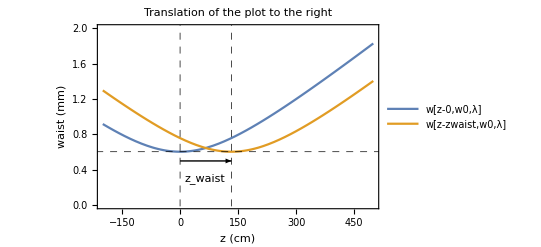

```mathematica
Module[{w0,zwaist,zcm,z,λ,zRayleigh},
λ=655 10^-9;
w0=0.0006042744933010027;
zwaist=1.3271969822526328;
zRayleigh = zR[w0,λ] ;
z=zcm 10^-2;

Print["Rayleigh lenght z_Reyleigh = ",zRayleigh 10^2," cm"];

Plot[{w[z-0,w0,λ] 10^3,w[z-zwaist,w0,λ] 10^3},{zcm,-200,500},Frame->True,Axes->None,FrameLabel->{"z (cm)","waist (mm)"},PlotLabel->Style["Translation of the plot to the right"],PlotLegends->{"w[z-0,w0,λ]","w[z-zwaist,w0,λ]"},GridLines->{{0,zwaist 10^2},{w0 10^3}},GridLinesStyle->Directive[Black, Dashed],PlotRange->{0,2},
Epilog->{
Text[Framed["z_waist"],{65,0.3}],
Arrow[{{0,0.5},{zwaist 10^2,0.5}}]
}]

]
```

We see that by doing this, we move the focus of the beam further along the beam path. It means that if we start traveling along the beam at z = 0, the beam will initially become smaller. This distance z_0 is what we have measured in the previous section of this notebook. It tells us in practice how far away the focus is from out z=0. If we also know the waist of the beam in the focus, we have the full information of the beam.

### Gaussian beam definitions, matrix formalism

This is just some definitions I use in the following sections. You can add/define your own matrices if needed, you can find most of them on Wikipedia. The exact formulation and semantics used here I just copied from Rainer Kaltenbaek.

For now, just initialize them and go to the next section.

```mathematica
zR[w0_,λ_]:=(π w0^2)/λ (*Rayleigh lenght*)
```

```mathematica
w0[zR_,λ_]:=√((λ zR)/π) (*waist in the focus of the gaussian beam*)
```

For calculating the waist at a given point, I now change the definition of w[...] to have complex beam parameter for input parameter. This is no new physics, just a different way to tell the function the same thing.

```mathematica
w[q_,λ_]:=w0[Im[q],λ] √(1+(Re[q]/Im[q])^2)(*if in material, devide λ by n*)
```

```mathematica
qNew[A_,qOld_]:=(A[[1,1]] qOld+A[[1,2]])/(A[[2,1]] qOld + A[[2,2]])
```

```mathematica
Mlens[f_]:={{1,0},{-1/f,1}}
```

```mathematica
Mfree[L_]:={{1,L},{0,1}}
```

```mathematica
Mref[n1_,n2_]:={{1,0},{0,n1/n2}}
```

```mathematica
MCurveRef[n1_,n2_,R_]:={{1,0},{(n1-n2)/(R n2),n1/n2}}
```

### 02 Sticking two plots together (going left to right)

Our main goal is to model changes of the gaussian beam along the beam path, like seeing what happens if we put in a lens or an optically denser material. In order to do this, we will use matrix formalism. The general explanation for matrix formalism is easily understandable for ray optics. There you can easily see that the ray propagation can be described through a system of linear equations. Thus matrices. We can do a similar thing with a gaussian beam, using the same matrices, just using a different initial vector, one that describes the gaussian beam. This vector describes the complex beam parameter we use to characterize our gaussian beam. Real part of this vector is the distance from the beam focus, while the imaginary part is the beam’s Rayleigh length.

q = z + ι z_R

Equations in the previous section describe this. If interested, take a look, or just use them as a definition.

Now to the important part. In order to see the beam propagation through our setup, we need to split it into individual sections, which we then stick together. Let’s look at a simple example. I want to use my RED beam I characterized in the previous sections and send it through a lens with a focal length of f = 100 mm. I will start tracking the beam at z = 0, move for a distance z_1 = 150 mm, go through a lens, and then travel additional z_2 = 300 mm. Let’s look at how I do it and then discuss the basic components:

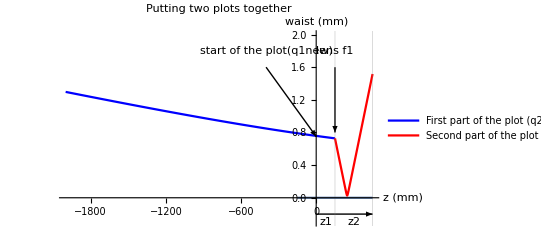

```mathematica
Module[{λ,w0initial,zwaist,zRayleighInitial,
focus1,
focus1mm,
z1,z2,
z1mm,z2mm,
z1plot,z2plot,
z1plotmm,z2plotmm,
qOld,q1new,q2new,q3new,q4new,
q2newplot,q4newplot,
plot},

(*initial RED beam, gives me inital q *)
λ=655 10^-9;
w0initial=0.0006042744933010027;
zwaist=1.3271969822526328;
zRayleighInitial = zR[w0initial,λ] ;

qOld=(0-zwaist)+I zRayleighInitial;
q1new=qNew[Mfree[0],qOld];

(*RED beam going to the focusing lens f1*)
z1=z1mm 10^-3;
z1mm = 150;
q2new=qNew[Mfree[z1],q1new];
z1plot=z1plotmm 10^-3;
q2newplot=qNew[Mfree[z1plot-0],q1new];

(*RED beam right after focusing lens*)
focus1=focus1mm 10^-3;
focus1mm=100 ;
q3new=qNew[Mlens[focus1],q2new];

(*RED beam traveling after the focusing lens*)
z2=z2mm 10^-3;
z2mm = 300;
q4new=qNew[Mfree[z2],q3new];
z2plot=z2plotmm 10^-3;
q4newplot=qNew[Mfree[z2plot-(z1)],q3new];

(* --------------------------------------------------------------------------*)
plot=Show[
Plot[{0},{x,-150,z1mm+z2mm}],(*just to initaly prepare the plot*)
Plot[w[q2newplot,λ] 10^3,{z1plotmm,-2000,z1mm},PlotStyle->{Blue}],(*RED beam to the first lens f1mm*)
Plot[w[q4newplot,λ] 10^3,{z2plotmm,z1mm,z1mm+z2mm},PlotStyle->{Red}],(*RED beam after the first lens f1mm*)
AxesLabel->{"z (mm)","waist (mm)"},
PlotLabel->Style["Putting two plots together"],
GridLines->{{z1mm,z1mm+z2mm},{0}},
PlotRange->{-0.3,2},
Epilog->{
Text[Framed["start of the plot(q1new)"],{-400,1.8}],
Arrow[{{-400,1.6},{0,0.75}}],
Text[Framed["lens f1"],{z1mm,1.8}],
Arrow[{{z1mm,1.6},{z1mm,0.8}}],
Arrow[{{0,-0.2},{z1mm+z2mm,-0.2}}],
Text["z1",{z1mm/2,-0.3}],
Text["z2",{z1mm+z2mm/2,-0.3}]
}
];
Legended[plot,LineLegend[{Blue, Red},{"First part of the plot (q2newplot)","Second part of the plot (q4newplot)"}]]
]
```

There are two sections to the above module.

First part tracks the complex beam parameter (vector) through the setup. The most important thing is to have the initial vector properly defined. Be careful of a minus signs, units, right wavelength, etc. “q1new” is the vector you have at the point z= 0 on the table (which you defined in the initial characterization! Keep track of that).

I then follow the beam through the setup, calculating new q2new, q3new... as we go along. In the sections where we have propagation through space (Mfree), I also include an additional identical step, with a new variable z1plot, z2plot,... This variable does not have a fixed value and is used for plotting. You also need to acknowledge that each new section will begin at some non-zero 0, this is why I use “z2plot-(z1)” for example. If you are confused about this, think about the edge cases where zplot2 = {z1 , z2} and try to relate it to the plot.

The second part is plotting the whole thing. Or sticking it together. This is the part where you will probably initially do some errors. Try to play with plotting limits, ± signs, etc. If you have kept track of what is happening with your q and not messed up any variables, it should work. The first part of the plotting sections plots consecutive sections along the beam part. Each section is between two regions, for example between z1 and z1+z2. Values between these two edge cases will be assigned to the variable z2plot. For the purpose of this section, I have colored the two sections differently, but as you will see later, one beam should have one color assigned to it.
It is good practice to use GridLines to visually split different sections of the plot

Last part of the plotting section is the Epilog. I use this here for the tutorial to plot the arrows and text boxes, but you don’t actually need this. It is maybe useful to mark the z1, z2 to individual sections, just so you know what is happening. Maybe also where f1, f2,... are.

### 03 Sticking two plots together (going from right to left)

Sometimes you will need to propagate one beam in one direction and another in the opposite direction and then maybe try to match them. Let’s first look at how to plot the same beam propagation as above, just starting at a different point (z1+z2) and going in the opposite direction.

Initial beam definition will be the same, you will just need to acknowledge the different propagation direction by changing zwaist to -zwaist. All propagations through space will need to become negative z2 -> -z2. You also need to switch the order of the variables in the z2plot-(z1+z2) section (just look at the example bellow). Any lenses will also need to be assigned a negative focal length, since the focal point is in the negative direction.
There is a lot ways to do this, but I suggest this one, because it will make sense later, when we really start to stick stuff together.

zwaist --> - zwaist
z1 -> -z1 (going in the other direction)
focus -> - focus (focal point will now be on the left)
q2newplot -> switch the order of (z1) and (z1+z2) before the z2plot (we start ploting from the right)

If this is done correctly, the plotting section should remain exactly the same as before, which will be useful later. There, the plotting section will be the one reference that will always make sense and you will be able to determine the missing signs, etc. in reference to it.

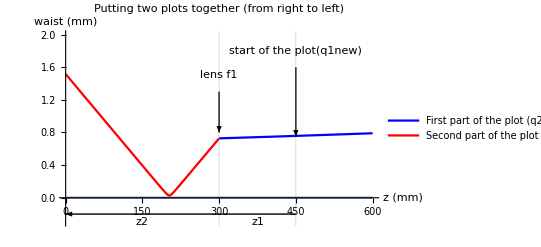

```mathematica
Module[{λ,w0initial,zwaist,zRayleighInitial,
focus1,
focus1mm,
z1,z2,
z1mm,z2mm,
z1plot,z2plot,
z1plotmm,z2plotmm,
qOld,q1new,q2new,q3new,q4new,
q2newplot,q4newplot,
plot},

(*initial RED beam*)
λ=655 10^-9;
w0initial=0.0006042744933010027;
zwaist=1.3271969822526328;
zRayleighInitial = zR[w0initial,λ] ;

qOld=(0+zwaist)+I zRayleighInitial;
q1new=qNew[Mfree[0],qOld];

(*RED beam traveling to the focusing lens:*)
z1=z1mm 10^-3;
z1mm = 150;
q2new=qNew[Mfree[-z1],q1new];
z1plot=z1plotmm 10^-3;
q2newplot=qNew[Mfree[z1plot-(z1+z2)],q1new];

(*RED beam right after focusing lens*)
focus1=focus1mm 10^-3;
focus1mm=-100 ;
q3new=qNew[Mlens[focus1],q2new];

(*RED beam traveling after the focusing lens:*)
z2=z2mm 10^-3;
z2mm = 300;
q4new=qNew[Mfree[-z2],q3new];
z2plot=z2plotmm 10^-3;
q4newplot=qNew[Mfree[z2plot-(z2)],q3new];
(* --------------------------------------------------------------------------*)
plot=Show[
Plot[{0},{x,0,z1mm+z2mm+150}],(*just to initaly prepare the plot*)
Plot[w[q2newplot,λ] 10^3,{z1plotmm,z2mm,z1mm+z2mm+150},PlotStyle->{Blue}],
Plot[w[q4newplot,λ] 10^3,{z2plotmm,0,z2mm},PlotStyle->{Red}],
AxesLabel->{"z (mm)","waist (mm)"},
PlotLabel->Style["Putting two plots together (from right to left)"],
GridLines->{{0,z2mm,z1mm+z2mm},{0}},PlotRange->{-0.3,2},
Epilog->{
Text[Framed["start of the plot(q1new)"],{z1mm+z2mm,1.8}],
Arrow[{{z1mm+z2mm,1.6},{z1mm+z2mm,0.75}}],
Text[Framed["lens f1"],{z2mm,1.5}],
Arrow[{{z2mm,1.3},{z2mm,0.8}}],
Arrow[{{z1mm+z2mm,-0.2},{0,-0.2}}],
Text["z1",{z2mm+z1mm/2,-0.3}],
Text["z2",{z2mm/2,-0.3}]
}
];
Legended[plot,LineLegend[{Blue, Red},{"First part of the plot (q2newplot)","Second part of the plot (q4newplot)"}]]
]
```

Just a small side note: to be really clear about what is happening, I have kept the order z1 and z2 as they were in the previous section. Later z1, z2,... will always go from left to right, and everything else will adapt to it.

### 03 Mode matching of different beams

Let’s now go to the fun stuff. I want to propagate two or more beams in different directions all on the same plot. Let’s consider a practical example where I get light out of a fibre collimated and send it across the table. Then I want to couple it into a bare fibre. I will need to use one or more lenses in right positions, to match the waist AND the divergence angle of the bare fibre mode. In other words, in order to efficiently couple light into a fibre, I will need to mode match my initial light to the mode of the fibre, which I will model, by plotting it as a beam going out of the fibre in the other direction.

For demonstration purposes I will use the same RED beam as before and two lenses, to couple into a fibre with a core diameter of 25 μm (might not make sense in reality, doesn’t matter).

Some warnings: The beams will now be going in two directions, but you only need to define each variable only once (z1, z2, f1,...). For different beams you should have same names/numbers for complex beam parameters in the same sections (qnew2 in z1,... ).

I recommend you write everything for one beam going from left to right, plot it, and then use the plotting section to keep track of the stuff for back propagation, changing what needs to be changed. It is also highly recommended you manage the naming of all variables systematically.

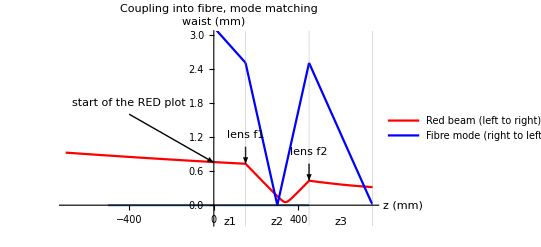

```mathematica
Module[{λRED,w0initialRED,zwaistRED,zRayleighInitialRED,
λFIBRE,w0initialFIBRE,zwaistFIBRE,zRayleighInitialFIBRE,
focus1,focus2,
focus1mm,focus2mm,
z1,z2,z3,
z1mm,z2mm,z3mm,
z1plot,z2plot,z3plot,
z1plotmm,z2plotmm,z3plotmm,
qOldRED,q1newRED,q2newRED,q3newRED,q4newRED,q5newRED,q6newRED,
qOldFIBRE,q1newFIBRE,q2newFIBRE,q3newFIBRE,q4newFIBRE,q5newFIBRE,q6newFIBRE,q7newFIBRE,
q2newREDplot,q4newREDplot,q6newREDplot,
q2newFIBREplot,q4newFIBREplot,q6newFIBREplot,
plot},
(*------------- RED BEAM --------------------*)
(*initial RED beam, gives me inital q *)
λRED=655 10^-9;
w0initialRED=0.0006042744933010027;
zwaistRED=1.3271969822526328;
zRayleighInitialRED = zR[w0initialRED,λRED] ;

qOldRED=(0-zwaistRED)+I zRayleighInitialRED;
q1newRED=qNew[Mfree[0],qOldRED];

(*RED beam going to first focusing lens f1*)
z1=z1mm 10^-3;
z1mm = 150;
q2newRED=qNew[Mfree[z1],q1newRED];
z1plot=z1plotmm 10^-3;
q2newREDplot=qNew[Mfree[z1plot-0],q1newRED];

(*RED beam right after first focusing lens f1*)
focus1=focus1mm 10^-3;
focus1mm=200 ;
q3newRED=qNew[Mlens[focus1],q2newRED];

(*RED beam traveling from first focusing lens f1 to second focusing lens f2*)
z2=z2mm 10^-3;
z2mm = 300;
q4newRED=qNew[Mfree[z2],q3newRED];
z2plot=z2plotmm 10^-3;
q4newREDplot=qNew[Mfree[z2plot-(z1)],q3newRED];

(*RED beam right after second focusing lens f2*)
focus2=focus2mm 10^-3;
focus2mm=100 ;
q5newRED=qNew[Mlens[focus2],q4newRED];

(*RED beam traveling from second focusing lens f2 to the bare fibre*)
z3=z3mm 10^-3;
z3mm = 300;
q6newRED=qNew[Mfree[z3],q5newRED];
z3plot=z3plotmm 10^-3;
q6newREDplot=qNew[Mfree[z3plot-(z1+z2)],q5newRED];

(*------------- FIBRE MODE --------------------*)
(*initial FIBRE beam/mode, gives me inital q *)
λFIBRE=655 10^-9;
w0initialFIBRE= 25 10^-6; (*I have arbitraly defined this*)
zwaistFIBRE=0; (*makes sense for a fibre tip*)
zRayleighInitialFIBRE = zR[w0initialFIBRE,λFIBRE] ;

qOldFIBRE=(0+zwaistFIBRE)+I zRayleighInitialFIBRE;
q7newFIBRE=qNew[Mfree[0],qOldFIBRE];

(*FIBRE beam traveling from the fibre tip to the second focusing lens f2*)
q6newFIBRE=qNew[Mfree[-z3],q7newFIBRE];
q6newFIBREplot=qNew[Mfree[z3plot-(z1+z2+z3)],q7newFIBRE];

(*FIBRE beam right after second focusing lens f2*)
q5newFIBRE=qNew[Mlens[-focus2],q6newFIBRE];

(*FIBRE beam traveling from second focusing lens f2 to first focusing lens f1*)
q4newFIBRE=qNew[Mfree[-z2],q5newFIBRE];
q4newFIBREplot=qNew[Mfree[z2plot-(z1+z2)],q5newFIBRE];

(*FIBRE beam right after first focusing lens f1*)
q3newFIBRE=qNew[Mlens[-focus1],q4newFIBRE];

(*FIBRE beam going from the first focusing lens f1 to z = 0*)
q2newFIBRE=qNew[Mfree[-z1],q3newFIBRE];
q2newFIBREplot=qNew[Mfree[z1plot-(z1)],q3newFIBRE];

(* --------------------------------------------------------------------------*)
plot=Show[
Plot[{0},{x,-500,z1mm+z2mm}],(*just to initaly prepare the plot*)
Plot[w[q2newREDplot,λRED] 10^3,{z1plotmm,-700,z1mm},PlotStyle->{Red}],(*RED beam to the first lens f1*)
Plot[w[q2newFIBREplot,λFIBRE] 10^3,{z1plotmm,-700,z1mm},PlotStyle->{Blue}],(*FIBRE beam from the first lens f1 to origin*)
Plot[w[q4newREDplot,λRED] 10^3,{z2plotmm,z1mm,z1mm+z2mm},PlotStyle->{Red}],(*RED beam between the first lens f1 and second lens f2*)
Plot[w[q4newFIBREplot,λFIBRE] 10^3,{z2plotmm,z1mm,z1mm+z2mm},PlotStyle->{Blue}],(*FIBRE beam between the second lens f2 and first lens f1*)
Plot[w[q6newREDplot,λRED] 10^3,{z3plotmm,z1mm+z2mm,z1mm+z2mm+z3mm},PlotStyle->{Red}],(*RED beam between second lens f2 and the fibre*)
Plot[w[q6newFIBREplot,λFIBRE] 10^3,{z3plotmm,z1mm+z2mm,z1mm+z2mm+z3mm},PlotStyle->{Blue}],(*FIBRE beam between fibre and second lens f2*)
AxesLabel->{"z (mm)","waist (mm)"},
PlotLabel->Style["Coupling into fibre, mode matching"],
GridLines->{{z1mm,z1mm+z2mm,z1mm+z2mm+z3mm},{0}},
PlotRange->{-0.3,3},
Epilog->{
Text[Framed["start of the RED plot"],{-400,1.8}],
Arrow[{{-400,1.6},{0,0.75}}],
Text[Framed["lens f1"],{z1mm,w[q2newRED,λRED] 10^3+0.5}],
Arrow[{{z1mm,w[q2newRED,λRED] 10^3+0.3},{z1mm,w[q2newRED,λRED] 10^3}}],
Text[Framed["lens f2"],{z1mm+z2mm,w[q4newRED,λRED] 10^3+0.5}],
Arrow[{{z1mm+z2mm,w[q4newRED,λRED] 10^3+0.3},{z1mm+z2mm,w[q4newRED,λRED] 10^3}}],

Text["z1",{z1mm/2,-0.3}],
Text["z2",{z1mm+z2mm/2,-0.3}],
Text["z3",{z1mm+z2mm+z3mm/2,-0.3}]
}
];
Legended[plot,LineLegend[{Red,Blue},{"Red beam (left to right)","Fibre mode (right to left)"}]]
]
```

Whopsy, this does not look like it matches. Of course it does not, since I just made up all the numbers. How do we now optimize? Well, we change the numbers until the modes match. For this, we define the above plot as a function of the unknown variables (z1, z2, z3, f1, f2) and call it through Manipulate function. This allows for a simple and straightforward way towards optimization. (Notice I now commented out the numbers that are optimized through Manipulate[...])

```mathematica
OptimisationFunction[focus1mm_,focus2mm_,z1mm_,z2mm_,z3mm_]:= Module[{λRED,w0initialRED,zwaistRED,zRayleighInitialRED,
λFIBRE,w0initialFIBRE,zwaistFIBRE,zRayleighInitialFIBRE,
focus1,focus2,
(*focus1mm,focus2mm,*)
z1,z2,z3,
(*z1mm,z2mm,z3mm,*)
z1plot,z2plot,z3plot,
z1plotmm,z2plotmm,z3plotmm,
qOldRED,q1newRED,q2newRED,q3newRED,q4newRED,q5newRED,q6newRED,
qOldFIBRE,q1newFIBRE,q2newFIBRE,q3newFIBRE,q4newFIBRE,q5newFIBRE,q6newFIBRE,q7newFIBRE,
q2newREDplot,q4newREDplot,q6newREDplot,
q2newFIBREplot,q4newFIBREplot,q6newFIBREplot,
plot},
(*------------- RED BEAM --------------------*)
(*initial RED beam, gives me inital q *)
λRED=655 10^-9;
w0initialRED=0.0006042744933010027;
zwaistRED=1.3271969822526328;
zRayleighInitialRED = zR[w0initialRED,λRED] ;

qOldRED=(0-zwaistRED)+I zRayleighInitialRED;
q1newRED=qNew[Mfree[0],qOldRED];

(*RED beam going to first focusing lens f1*)
z1=z1mm 10^-3;
(*z1mm = 150; FREE PARAMETER*)
q2newRED=qNew[Mfree[z1],q1newRED];
z1plot=z1plotmm 10^-3;
q2newREDplot=qNew[Mfree[z1plot-0],q1newRED];

(*RED beam right after first focusing lens f1*)
focus1=focus1mm 10^-3;
(*focus1mm=200 ; FREE PARANETER*)
q3newRED=qNew[Mlens[focus1],q2newRED];

(*RED beam traveling from first focusing lens f1 to second focusing lens f2*)
z2=z2mm 10^-3;
(*z2mm = 300; FREE PARAMETER*)
q4newRED=qNew[Mfree[z2],q3newRED];
z2plot=z2plotmm 10^-3;
q4newREDplot=qNew[Mfree[z2plot-(z1)],q3newRED];

(*RED beam right after second focusing lens f2*)
focus2=focus2mm 10^-3;
(*focus2mm=100; FREE PARAMETER*)
q5newRED=qNew[Mref[ns[sasd,asdas],1],q4newRED];

(*RED beam traveling from second focusing lens f2 to the bare fibre*)
z3=z3mm 10^-3;
(*z3mm = 300; FREE PARAMETER*)
q6newRED=qNew[Mfree[z3],q5newRED];
z3plot=z3plotmm 10^-3;
q6newREDplot=qNew[Mfree[z3plot-(z1+z2)],q5newRED];

(*------------- FIBRE MODE --------------------*)
(*initial FIBRE beam/mode, gives me inital q *)
λFIBRE=655 10^-9;
w0initialFIBRE= 25 10^-6; (*I have arbitraly defined this*)
zwaistFIBRE=0; (*makes sense for a fibre tip*)
zRayleighInitialFIBRE = zR[w0initialFIBRE,λFIBRE] ;

qOldFIBRE=(0+zwaistFIBRE)+I zRayleighInitialFIBRE;
q7newFIBRE=qNew[Mfree[0],qOldFIBRE];

(*FIBRE beam traveling from the fibre tip to the second focusing lens f2*)
q6newFIBRE=qNew[Mfree[-z3],q7newFIBRE];
q6newFIBREplot=qNew[Mfree[z3plot-(z1+z2+z3)],q7newFIBRE];

(*FIBRE beam right after second focusing lens f2*)
q5newFIBRE=qNew[Mref[1,ns[wo,lambda]],q6newFIBRE];

(*FIBRE beam traveling from second focusing lens f2 to first focusing lens f1*)
q4newFIBRE=qNew[Mfree[-z2],q5newFIBRE];
q4newFIBREplot=qNew[Mfree[z2plot-(z1+z2)],q5newFIBRE];

(*FIBRE beam right after first focusing lens f1*)
q3newFIBRE=qNew[Mlens[-focus1],q4newFIBRE];

(*FIBRE beam going from the first focusing lens f1 to z = 0*)
q2newFIBRE=qNew[Mfree[-z1],q3newFIBRE];
q2newFIBREplot=qNew[Mfree[z1plot-(z1)],q3newFIBRE];

(* --------------------------------------------------------------------------*)
plot=Show[
Plot[{0},{x,-500,z1mm+z2mm}],(*just to initaly prepare the plot*)
Plot[w[q2newREDplot,λRED] 10^3,{z1plotmm,-700,z1mm},PlotStyle->{Red}],(*RED beam to the first lens f1*)
Plot[w[q2newFIBREplot,λFIBRE] 10^3,{z1plotmm,-700,z1mm},PlotStyle->{Blue}],(*FIBRE beam from the first lens f1 to origin*)
Plot[w[q4newREDplot,λRED] 10^3,{z2plotmm,z1mm,z1mm+z2mm},PlotStyle->{Red}],(*RED beam between the first lens f1 and second lens f2*)
Plot[w[q4newFIBREplot,λFIBRE] 10^3,{z2plotmm,z1mm,z1mm+z2mm},PlotStyle->{Blue}],(*FIBRE beam between the second lens f2 and first lens f1*)
Plot[w[q6newREDplot,λRED] 10^3,{z3plotmm,z1mm+z2mm,z1mm+z2mm+z3mm},PlotStyle->{Red}],(*RED beam between second lens f2 and the fibre*)
Plot[w[q6newFIBREplot,λFIBRE] 10^3,{z3plotmm,z1mm+z2mm,z1mm+z2mm+z3mm},PlotStyle->{Blue}],(*FIBRE beam between fibre and second lens f2*)
AxesLabel->{"z (mm)","waist (mm)"},
PlotLabel->Style["Coupling into fibre, mode matching"],
GridLines->{{z1mm,z1mm+z2mm,z1mm+z2mm+z3mm},{0}},
PlotRange->{-0.3,3},
Epilog->{
Text[Framed["start of the RED plot"],{-400,1.8}],
Arrow[{{-400,1.6},{0,0.75}}],
Text[Framed["lens f1"],{z1mm,w[q2newRED,λRED] 10^3+0.5}],
Arrow[{{z1mm,w[q2newRED,λRED] 10^3+0.3},{z1mm,w[q2newRED,λRED] 10^3}}],
Text[Framed["lens f2"],{z1mm+z2mm,w[q4newRED,λRED] 10^3+0.5}],
Arrow[{{z1mm+z2mm,w[q4newRED,λRED] 10^3+0.3},{z1mm+z2mm,w[q4newRED,λRED] 10^3}}],

Text["z1",{z1mm/2,-0.3}],
Text["z2",{z1mm+z2mm/2,-0.3}],
Text["z3",{z1mm+z2mm+z3mm/2,-0.3}]
}
];
Legended[plot,LineLegend[{Red,Blue},{"Red beam (left to right)","Fibre mode (right to left)"}]]
]
```

Let's now call this through Manipulate[...]. Initial plot you will see will be the one for the initially assigned values (f1 = 200 mm,...). Now play with the sliders until you manage to completely overlap the blue and the red lines.

```mathematica
Manipulate[OptimisationFunction[focus1mm,focus2mm,z1mm,z2mm,z3mm],
{{focus1mm,200},10,200},
{{focus2mm,100},10,200},
{{z1mm,150},1,500},
{{z2mm,300},1,500},
{{z3mm,300},1,500}
]
```

You have noticed that some parameters are more important than others. A few things to note. For lenses, you can only use values that you have available in the lab, or that you can buy. This are not random numbers. For distances, you are limited by the room on the optical table. You should always acknowledge clipping conditions, etc.
Of course you will never manage to get perfect alignment, if only because all this runs on finite precision Mathematica calculations. BUT, real life includes imperfections and of course you cannot assume that the numbers you get from this will be exactly what you need on the table. This method will tell you which lenses to use and at which positions to put them. You will then need to further optimize the coupling in reference to a live signal you have. But you should already be close.

For example, this is what I got in 30 second of walking the sliders around:

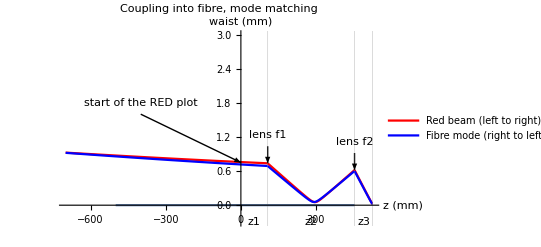

```mathematica
OptimisationFunction[200,50,107,347,72]
```

This plot would tell me that I would need to use 200mm and 50 mm lense at approximately above positions to effectively couple RED light into a fibre with diameter 24 μm.

You can use this approach to couple into a fibre, a crystal or even a cavity. You can use it to determine which lenses to use at which distances to collimate your laser beam to the required waist.

### 04 Beam propagation in optically denser materials n≠1

A small warning worth talking about separately. Image sending a beam through a nonlinear crystal, or even any optically denser material. You can follow the above described plotting approach, but you need to acknowledge that the wavelength in the optically denser material changes!

Let’s first look at how not to do it. I will send my good old RED beam into a nonlinear crystal with n = 2.6,  travel for 30 mm inside, and then send it out again:

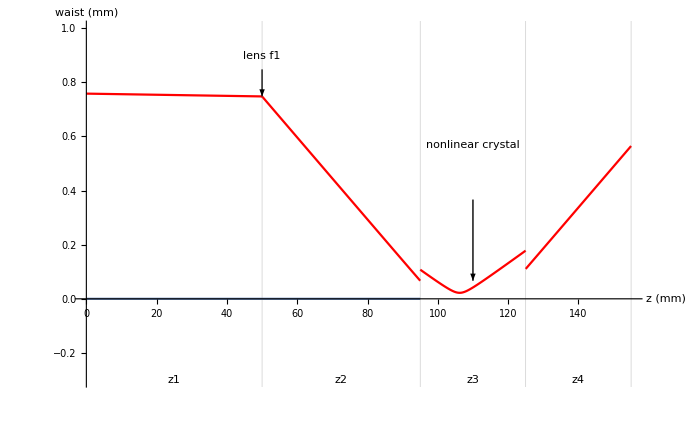

```mathematica
Module[{λRED,w0initialRED,zwaistRED,zRayleighInitialRED,
focus1,
focus1mm,
n,
z1,z2,z3,z4,
z1mm,z2mm,z3mm,z4mm,
z1plot,z2plot,z3plot,z4plot,
z1plotmm,z2plotmm,z3plotmm,z4plotmm,
qOldRED,q1newRED,q2newRED,q3newRED,q4newRED,q5newRED,q6newRED,q7newRED,q8newRED,
q2newREDplot,q4newREDplot,q6newREDplot,q8newREDplot,
plot},
(*------------- RED BEAM --------------------*)
(*initial RED beam, gives me inital q *)
λRED=655 10^-9;
w0initialRED=0.0006042744933010027;
zwaistRED=1.3271969822526328;
zRayleighInitialRED = zR[w0initialRED,λRED] ;

qOldRED=(0-zwaistRED)+I zRayleighInitialRED;
q1newRED=qNew[Mfree[0],qOldRED];

(*RED beam going to first focusing lens f1*)
z1=z1mm 10^-3;
z1mm = 50;
q2newRED=qNew[Mfree[z1],q1newRED];
z1plot=z1plotmm 10^-3;
q2newREDplot=qNew[Mfree[z1plot-0],q1newRED];

(*RED beam right after first focusing lens f1*)
focus1=focus1mm 10^-3;
focus1mm=50 ;
q3newRED=qNew[Mlens[focus1],q2newRED];

(*RED beam traveling from first focusing lens f1 to nonlinear crystal*)
z2=z2mm 10^-3;
z2mm = 45;
q4newRED=qNew[Mfree[z2],q3newRED];
z2plot=z2plotmm 10^-3;
q4newREDplot=qNew[Mfree[z2plot-(z1)],q3newRED];


(*RED beam right after difraction on crystal surface*)
n=2.6;
q5newRED=qNew[Mref[1,n],q4newRED];

(*RED beam traveling through the nonlinear crystal*)
z3=z3mm 10^-3;
z3mm = 30;
q6newRED=qNew[Mfree[z3],q5newRED];
z3plot=z3plotmm 10^-3;
q6newREDplot=qNew[Mfree[z3plot-(z1+z2)],q5newRED];

(*RED beam right after difraction on crystal surface*)
q7newRED=qNew[Mref[n,1],q6newRED];

(*RED beam traveling through glass*)
z4=z4mm 10^-3;
z4mm = 30;
q8newRED=qNew[Mfree[z4],q7newRED];
z4plot=z4plotmm 10^-3;
q8newREDplot=qNew[Mfree[z4plot-(z1+z2+z3)],q7newRED];

(* --------------------------------------------------------------------------*)
plot=Show[
Plot[{0},{x,0,z1mm+z2mm}],(*just to initaly prepare the plot*)
Plot[w[q2newREDplot,λRED] 10^3,{z1plotmm,0,z1mm},PlotStyle->{Red}],(*RED beam to the first lens f1*)
Plot[w[q4newREDplot,λRED] 10^3,{z2plotmm,z1mm,z1mm+z2mm},PlotStyle->{Red}],(*RED beam between the first lens f1 and second lens f2*)
Plot[w[q6newREDplot,λRED] 10^3,{z3plotmm,z1mm+z2mm,z1mm+z2mm+z3mm},PlotStyle->{Red}],(*RED beam between second lens f2 and the fibre*)
Plot[w[q8newREDplot,λRED] 10^3,{z4plotmm,z1mm+z2mm+z3mm,z1mm+z2mm+z3mm+z4mm},PlotStyle->{Red}],(*RED beam between second lens f2 and the fibre*)
AxesLabel->{"z (mm)","waist (mm)"},
PlotLabel->Style[""],
GridLines->{{z1mm,z1mm+z2mm,z1mm+z2mm+z3mm,z1mm+z2mm+z3mm+z4mm},{0}},
PlotRange->{-0.3,1},
Epilog->{
Text[Framed["lens f1"],{z1mm,w[q2newRED,λRED] 10^3+0.15}],
Arrow[{{z1mm,w[q2newRED,λRED] 10^3+0.1},{z1mm,w[q2newRED,λRED] 10^3}}],
Text[Framed["nonlinear crystal"],{z1mm+z2mm+z3mm/2,w[q4newRED,λRED] 10^3+0.5}],
Arrow[{{z1mm+z2mm+z3mm/2,w[q4newRED,λRED] 10^3+0.3},{z1mm+z2mm+z3mm/2,w[q4newRED,λRED] 10^3}}],

Text["z1",{z1mm/2,-0.3}],
Text["z2",{z1mm+z2mm/2,-0.3}],
Text["z3",{z1mm+z2mm+z3mm/2,-0.3}],
Text["z4",{z1mm+z2mm+z3mm+z4mm/2,-0.3}]
}
]
]
```

See how the beam waist at the crystal edges does not match? It should. So what did we do wrong? We forgot that λ changes in optically denser medium. In the z3 region, we should correct the plot function from “w[q6newREDplot,λRED]” to “w[q6newREDplot,λRED/n]”. This is the only change I will do now in the next Module[...]:

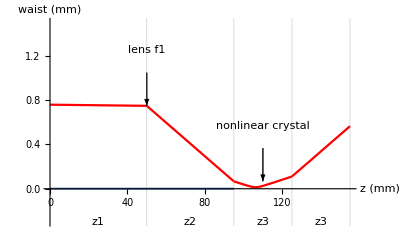

```mathematica
Module[{λRED,w0initialRED,zwaistRED,zRayleighInitialRED,
focus1,
focus1mm,
n,
z1,z2,z3,z4,
z1mm,z2mm,z3mm,z4mm,
z1plot,z2plot,z3plot,z4plot,
z1plotmm,z2plotmm,z3plotmm,z4plotmm,
qOldRED,q1newRED,q2newRED,q3newRED,q4newRED,q5newRED,q6newRED,q7newRED,q8newRED,
q2newREDplot,q4newREDplot,q6newREDplot,q8newREDplot,
plot},
(*------------- RED BEAM --------------------*)
(*initial RED beam, gives me inital q *)
λRED=655 10^-9;
w0initialRED=0.0006042744933010027;
zwaistRED=1.3271969822526328;
zRayleighInitialRED = zR[w0initialRED,λRED] ;

qOldRED=(0-zwaistRED)+I zRayleighInitialRED;
q1newRED=qNew[Mfree[0],qOldRED];

(*RED beam going to first focusing lens f1*)
z1=z1mm 10^-3;
z1mm = 50;
q2newRED=qNew[Mfree[z1],q1newRED];
z1plot=z1plotmm 10^-3;
q2newREDplot=qNew[Mfree[z1plot-0],q1newRED];

(*RED beam right after first focusing lens f1*)
focus1=focus1mm 10^-3;
focus1mm=50 ;
q3newRED=qNew[Mlens[focus1],q2newRED];

(*RED beam traveling from first focusing lens f1 to nonlinear crystal*)
z2=z2mm 10^-3;
z2mm = 45;
q4newRED=qNew[Mfree[z2],q3newRED];
z2plot=z2plotmm 10^-3;
q4newREDplot=qNew[Mfree[z2plot-(z1)],q3newRED];


(*RED beam right after difraction on crystal surface*)
n=2.6;
q5newRED=qNew[Mref[1,n],q4newRED];

(*RED beam traveling through the nonlinear crystal*)
z3=z3mm 10^-3;
z3mm = 30;
q6newRED=qNew[Mfree[z3],q5newRED];
z3plot=z3plotmm 10^-3;
q6newREDplot=qNew[Mfree[z3plot-(z1+z2)],q5newRED];

(*RED beam right after difraction on crystal surface*)
q7newRED=qNew[Mref[n,1],q6newRED];

(*RED beam traveling through glass*)
z4=z4mm 10^-3;
z4mm = 30;
q8newRED=qNew[Mfree[z4],q7newRED];
z4plot=z4plotmm 10^-3;
q8newREDplot=qNew[Mfree[z4plot-(z1+z2+z3)],q7newRED];

(* --------------------------------------------------------------------------*)
plot=Show[
Plot[{0},{x,0,z1mm+z2mm}],(*just to initaly prepare the plot*)
Plot[w[q2newREDplot,λRED] 10^3,{z1plotmm,0,z1mm},PlotStyle->{Red}],(*RED beam to the first lens f1*)
Plot[w[q4newREDplot,λRED] 10^3,{z2plotmm,z1mm,z1mm+z2mm},PlotStyle->{Red}],(*RED beam between the first lens f1 and second lens f2*)
Plot[w[q6newREDplot,λRED/n] 10^3,{z3plotmm,z1mm+z2mm,z1mm+z2mm+z3mm},PlotStyle->{Red}],(*RED beam between second lens f2 and the fibre*)
Plot[w[q8newREDplot,λRED] 10^3,{z4plotmm,z1mm+z2mm+z3mm,z1mm+z2mm+z3mm+z4mm},PlotStyle->{Red}],(*RED beam between second lens f2 and the fibre*)
AxesLabel->{"z (mm)","waist (mm)"},
PlotLabel->Style[""],
GridLines->{{z1mm,z1mm+z2mm,z1mm+z2mm+z3mm,z1mm+z2mm+z3mm+z4mm},{0}},
PlotRange->{-0.3,1.5},
Epilog->{
Text[Framed["lens f1"],{z1mm,w[q2newRED,λRED] 10^3+0.5}],
Arrow[{{z1mm,w[q2newRED,λRED] 10^3+0.3},{z1mm,w[q2newRED,λRED] 10^3}}],
Text[Framed["nonlinear crystal"],{z1mm+z2mm+z3mm/2,w[q4newRED,λRED] 10^3+0.5}],
Arrow[{{z1mm+z2mm+z3mm/2,w[q4newRED,λRED] 10^3+0.3},{z1mm+z2mm+z3mm/2,w[q4newRED,λRED] 10^3}}],

Text["z1",{z1mm/2,-0.3}],
Text["z2",{z1mm+z2mm/2,-0.3}],
Text["z3",{z1mm+z2mm+z3mm/2,-0.3}],
Text["z3",{z1mm+z2mm+z3mm+z4mm/2,-0.3}]
}
]
]
```

See? Now it matches! Just keep this in mind.

### 05 Extreme example. Coupling into a cavity

I will probably add this at some point.

Finding a cavity mode (calculate waist from lenght and curvature),...